```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/examples/sor_poisson_simple_test/solution.dat"];
data=Take[data,{2, data//Length} ];
```

```mathematica
ListPlot3D[data]
```

-Graphics3D-

```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/examples/sor_poisson_simple_test/custom_solution.dat"];
data=Take[data,{2, data//Length} ];
ListPlot3D[data, PlotRange->All]
```

-Graphics3D-

```mathematica
sigma[dx_, dy_, Nx_, Ny_]:=1/(1/(dx*dx)+1/(dy*dy))*(Cos[Pi/Nx]/(dx*dx)+Cos[Pi/Ny]/(dy*dy))
omega[dx_, dy_, Nx_, Ny_]:=2/(1+Sqrt[1-sigma[dx, dy, Nx, Ny]^2])
```

```mathematica
conData=Import["/home/jure/Documents/opengl_ucenje/examples/sor_poisson_simple_test/sor_convergence_data.dat"];
conData=Take[conData,{2, conData//Length}];
```

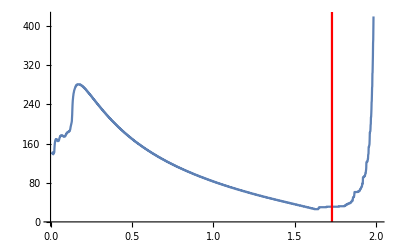

```mathematica
Show[
ListLinePlot[conData, PlotRange->Automatic],
ParametricPlot[{omega[0.01, 0.01, 20,20], y},{y,0,1000}, PlotStyle->Red]
]
```

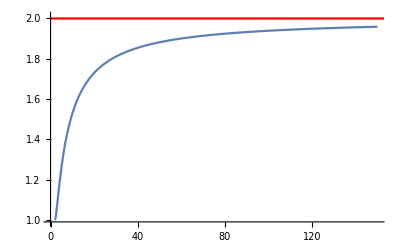

```mathematica
Show[
Plot[omega[0.1,0.1, size, size],{size,2,150}, PlotRange->{0.99,2.01}],
ParametricPlot[{x,2},{x,0,1000}, PlotRange->All, PlotStyle->Red]
]
```

```mathematica
sigma[dx_, dy_, Nx_, Ny_]:=1/(1/(dx*dx)+1/(dy*dy))*(Cos[Pi/Nx]/(dx*dx)+Cos[Pi/Ny]/(dy*dy))
omega[dx_, dy_, Nx_, Ny_]:=2/(1+Sqrt[1-sigma[dx, dy, Nx, Ny]^2])
```

```mathematica
sigma[0.001, 0.001, 40, 40]
omega[0.001, 0.001, 100, 100]
```

0.996917

1.93909

```mathematica
eigenvalueData=Import["/home/jure/Documents/opengl_ucenje/examples/sor_poisson_simple_test/sor_eigenvalue_approx.dat"];
eigenvalueData=Take[eigenvalueData,{2, eigenvalueData//Length}];
```

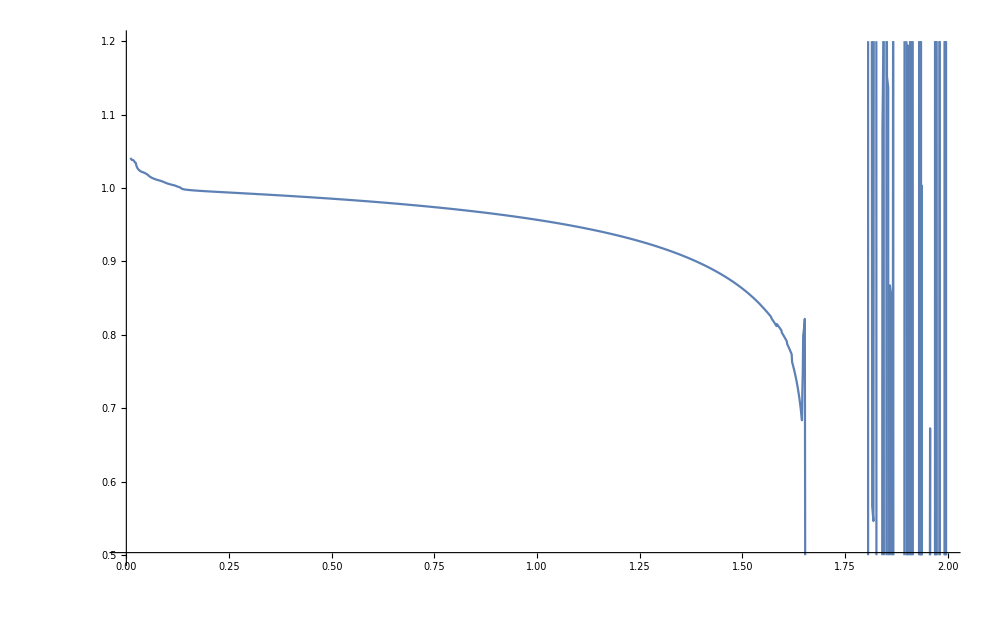

```mathematica
ListLinePlot[eigenvalueData, PlotRange->{{0,1.99},{0.5,1.2}}, ImageSize->1000]
```

```mathematica
tab1=Select[eigenvalueData, #[[1]]<1.99&];
omega1=tab1[[All,1]];
eig1=tab1[[All,2]];
maxEigenvalue=(1-omega1-eig1)/(omega1*Sqrt[eig1]);
maxEigenvalue//Mean;
tab2=Transpose[{omega1,Log[10, 0.0001]/Log[10,Abs[eig1]]}];
```

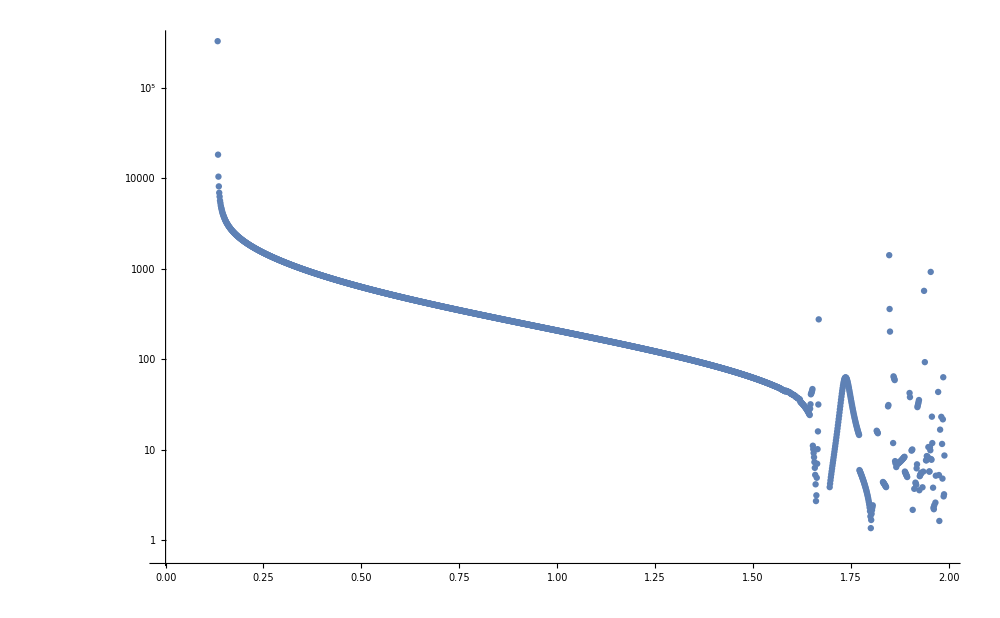

```mathematica
ListLogPlot[tab2, ImageSize->1000]
```